```mathematica
ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
dϕ[x_]:=If[Abs[x]>1,0,
			If[x==1 ,-1/2,
			If[x==-1,1/2,
			If[x==0,0,
			If[x>0,-1,1]]]]]
test[x_]:=Sin[Pi x]^2
dtest[x_]:=2 Pi Cos[Pi x] Sin[Pi x]
```

```mathematica
ceil[x_]:=1+Floor[x]
```

```mathematica
getCoefficient[f_,x_,l_]:=f[x]-1/2 f[x+2^-l]-1/2 f[x-2^-l]
hierarchicalCoefficients[f_,l_]:={{f[1],f[0]}}~Append~Table[Table[getCoefficient[f,2^-k i,k],{i,1,2^k-1,2}],{k,1,l}]

Reconstruct[coefficients_]:=If[#==1,coefficients[[1,1]],
coefficients[[1,1]]#+coefficients[[1,2]](1-#)+Sum[coefficients[[2,l,ceil[2^(l-1)#]]] ϕ[2^l(#-2^-l(2ceil[2^(l-1)#]-1))],{l,1,Length[coefficients[[2]]]}]]&

project[f_,l_]:=Reconstruct[hierarchicalCoefficients[f,l]]
```

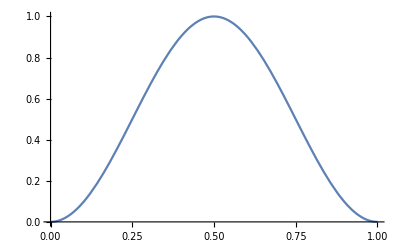

```mathematica
Plot[#[x],{x,0,1}]&[Reconstruct[N[hierarchicalCoefficients[Sin[Pi #]^2&,7]]]]
```

```mathematica
diff[f_,l_]:=If[#< 2^-l, diff[diff[f,l+1],l+1][2^-l]# (*(f[#+2^(-l-2)]-f[#])/2^(-l-2)*),If[#> 1-2^-l, diff[diff[f,l+1],l+1][1-2^-l](#-1),(f[#+2^-l]-f[#-2^-l])/(2 2^-l)]]&
```

```mathematica
(*dhierarchicalCoefficients[f_,l_]:=Table[Table[(getCoefficient[f,2^-k (i+1/4),k]+getCoefficient[f,2^-k (i-1/4),k])/2,{i,1,2^k-1,2}],{k,1,l}]

*)

dReconstruct[coefficients_]:=coefficients[[1,1]]-coefficients[[1,2]]+Sum[coefficients[[2,l,ceil[2^(l-1)#]]] 2^l   dϕ[2^l(#-2^-l(2ceil[2^(l-1)#]-1))],{l,1,Length[coefficients[[2]]]}]&
```

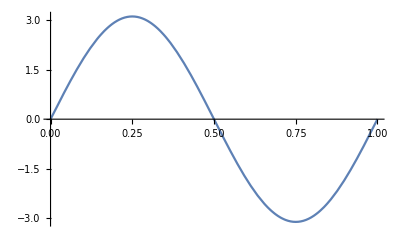

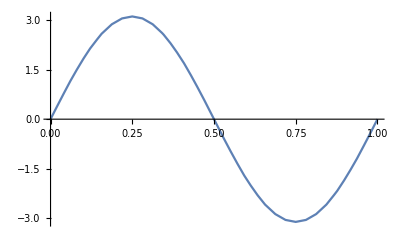

```mathematica
Plot[#[x],{x,0,1}]&[project[diff[project[test,7],5],7]]
Plot[#[x],{x,0,1}]&[project[diff[Reconstruct[hierarchicalCoefficients[test,7]],5],5]]
```

```mathematica
test2D[x_,y_]:=Sin[Pi x]^2Sin[Pi y]^2
dytest2D[x_,y_]:=2Pi Sin[Pi x]^2 Sin[Pi y] Cos[Pi y]
```

```mathematica
getCoefficient2D[f_,x_,y_,lx_,ly_]:=f[x,y]-1/2 f[x+2^-lx,y]-1/2 f[x-2^-lx,y]-1/2 f[x,y+2^-ly]-1/2 f[x,y-2^-ly]+1/4 f[x+2^-lx,y+2^-ly]+1/4 f[x-2^-lx,y+2^-ly]+1/4 f[x+2^-lx,y-2^-ly]+1/4 f[x-2^-lx,y-2^-ly]


hierarchicalCoefficients2D[f_,lx_,ly_]:=Table[Table[getCoefficient2D[f,2^-kx i,2^-ky j,kx,ky],{i,1,2^kx-1,2},{j,1,2^ky-1,2}],{kx,1,lx},{ky,1,ly}]

Reconstruct2D[coefficients_]:=Sum[coefficients[[lx,ly,ceil[2^(lx-1)#1],ceil[2^(ly-1)#2]]] ϕ[2^lx(#1-2^-lx(2ceil[2^(lx-1)#1]-1))] ϕ[2^ly(#2-2^-ly(2ceil[2^(ly-1)#2]-1))],{lx,1,Length[coefficients]},{ly,1,Length[coefficients[[lx]]]}]&

project2D[f_,lx_,ly_]:=Reconstruct2D[hierarchicalCoefficients2D[f,lx,ly]]
```

```mathematica
diffx[f_,l_]:=If[#1< 2^-l, diffx[diffx[f,l+1],l+1][2^-l,#2]#1,If[#1> 1-2^-l, diffx[diffx[f,l+1],l+1][1-2^-l,#2](#1-1),(f[#1+2^-l,#2]-f[#1-2^-l,#2])/(2 2^-l) ]]&

diffy[f_,l_]:=If[#2< 2^-l, diffy[diffy[f,l+1],l+1][#1,2^-l]#2,If[#2> 1-2^-l, diffy[diffy[f,l+1],l+1][#1,1-2^-l](#2-1),(f[#1,#2+2^-l]-f[#1,#2-2^-l])/(2 2^-l)]]&
```

```mathematica
Plot3D[#[x,y],{x,0,1},{y,0,1}]&[diffx[test2D,4]]
Plot3D[#[x,y],{x,0,1},{y,0,1}]&[diffx[project2D[test2D,5,5],4]]
```

-Graphics3D-

-Graphics3D-

```mathematica
Timing[NIntegrate[(#1[x,y]-#2[x,y])^2,{x,0,1},{y,0,1},PrecisionGoal->2]&[diffx[test2D,4],diffx[project2D[test2D,5,5],4]]]
```

{70.3685,0.0000414399}

```mathematica
Plot3D[#[x,y],{x,0,1},{y,0,1}]&[diffy[test2D,4]]
Plot3D[#[x,y],{x,0,1},{y,0,1}]&[diffy[project2D[test2D,5,5],4]]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*dxReconstruct2D[coefficients_]:=Sum[coefficients[[lx,ly,Ceiling[2^(lx-1)#],Ceiling[2^(ly-1)#]]] 2^lx dϕ[2^lx(#1-2^-lx(2Ceiling[2^(lx-1)#]-1))] ϕ[2^ly(#2-2^-ly(2Ceiling[2^(ly-1)#]-1))],{lx,1,Length[coefficients]},{ly,1,Length[coefficients[[lx]]]}]&


dyReconstruct2D[coefficients_]:=Sum[coefficients[[lx,ly,Ceiling[2^(lx-1)#],Ceiling[2^(ly-1)#]]] 2^ly ϕ[2^lx(#1-2^-lx(2Ceiling[2^(lx-1)#]-1))] dϕ[2^ly(#2-2^-ly(2Ceiling[2^(ly-1)#]-1))],{lx,1,Length[coefficients]},{ly,1,Length[coefficients[[lx]]]}]&



We don't need this anymore, and in fact it was never a good way to do differentiation. 
*)
```